```mathematica
link = Install[NotebookDirectory[]<>"bin/MathematicaPEntropy"]
```

LinkObject[…]

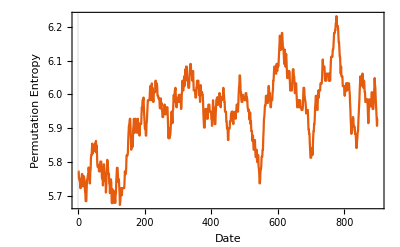

```mathematica
rand = RandomReal[{0,1},1000];
dates = Range[1000];
pentropy = PermutationEntropy[dates,rand,5,100];
ListLinePlot[pentropy, PlotTheme->"Scientific", FrameLabel->{"Date", "Permutation Entropy"}]
```